# Solving ODEs and DAEs with NDSolve

## Ordinary Differential Equations and Events

"Learning Objectives" |

Mathematica is a powerful tool for solving ordinary differential equations. This section covers:

Numerical methods to solve ordinary differential equations (ODEs) with NDSolve

Stiffness in differential equations

Including events in differential equations

Solving eigenvalue and boundary value problems with NDEigensystem

## ODE Methods

The Wolfram Language has a wide selection of methods available to solve ODEs. If no method is specified, NDSolve will analyze the equations and choose an appropriate method:

```mathematica
eqns={Y1'[t]==1-4Y1[t]+Y1[t]^2 Y2[t],Y2'[t]==3Y1[t]-Y1[t]^2 Y2[t]};
cond={Y1[0]==3/2,Y2[0]==3};
NDSolve[{eqns,cond},{Y1[t],Y2[t]},{t,0,20}]
```

{{Y1[t]→InterpolatingFunction[…][t],Y2[t]→InterpolatingFunction[…][t]}}

```mathematica
It is sometimes advantageous to pick a specific method. A few common ODE methods will be discussed in this section.
```

### Runge–Kutta

NDSolve can use the family of Runge–Kutta methods, both explicit and implicit. Runge–Kutta methods approximate the function at the next step using the formula:

g_i | == | y_n+h∑_(j=1) a_(i,j)k_j, | 
k_i | == | f(t_n+c_i h,g_i), | i==1,2,…,s,
y_(n+1) | == | y_n+h∑_(i=1)^s b_i k_i. | 

The sum in g_i runs from j=1 to j=i-1 in explicit methods, while in implicit methods the sum runs up to the order of the method, s:

```mathematica
NDSolve[{eqns,cond},{Y1[t],Y2[t]},{t,0,20},Method->"ImplicitRungeKutta"];
NDSolve[{eqns,cond},{Y1[t],Y2[t]},{t,0,20},Method->"ExplicitRungeKutta"];
```

The options and default values for the explicit and implicit Runge–Kutta methods are:

```mathematica
CellPrint@ExpressionCell[Grid[{{"\"ExplicitRungeKutta\" Options","\"ImplicitRungeKutta\" Options"},
{Options[NDSolve`ExplicitRungeKutta]//TableForm,
Options[NDSolve`ImplicitRungeKutta]//TableForm}},
Frame->All],"Output",GeneratedCell->False]
```

"ExplicitRungeKutta" Options | "ImplicitRungeKutta" Options
Coefficients→EmbeddedExplicitRungeKuttaCoefficients
DifferenceOrder→Automatic
EmbeddedDifferenceOrder→Automatic
StepSizeControlParameters→Automatic
StepSizeRatioBounds→{1/8,4}
StepSizeSafetyFactors→Automatic
StiffnessTest→Automatic | Coefficients→ImplicitRungeKuttaGaussCoefficients
DifferenceOrder→Automatic
ImplicitSolver→Newton
StepSizeControlParameters→Automatic
StepSizeRatioBounds→{1/8,4}
StepSizeSafetyFactors→Automatic

For a detailed discussion of these methods, other explicit and implicit methods, their implementation, and options, see the NDSolve tutorial.

```mathematica
Clear["Global`*"]
```

## Stiffness

A stiff equation is a differential equation for which certain numerical methods are unstable unless the step size is taken to be extremely small.

Unlike a singularity, stiffness is an accuracy and precision issue. For better efficiency, implicit methods are often used instead to deal with stiff equations.

Robertson’s equation for modeling chemical reactions is an example of a stiff equation:

```mathematica
eqns={Y1'[t]==-1/25 Y1[t]+10000Y2[t]Y3[t],
Y2'[t]==Y1[t]/25-30000000 Y2[t]^2-10000Y2[t]Y3[t],Y3'[t]==30000000 Y2[t]^2};
```

```mathematica
cond={Y1[0]==1,Y2[0]==0,Y3[0]==0};
```

Since the system is stiff, an explicit method normally will not work:

```mathematica
NDSolve[{eqns,cond},{Y1[t],Y2[t],Y3[t]},{t,0,10},Method->"ExplicitRungeKutta"];
```

NDSolve::ndstf: At t == 0.0102397, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

Try an implicit method instead:

```mathematica
AbsoluteTiming[NDSolve[{eqns,cond},{Y1[t],Y2[t],Y3[t]},{t,0,10},Method->"ImplicitRungeKutta"]]
```

{0.433477,{{Y1[t]→InterpolatingFunction[…][t],Y2[t]→InterpolatingFunction[…][t],Y3[t]→InterpolatingFunction[…][t]}}}

Implicit methods are slow, so it is not ideal to use an implicit method exclusively, even with a stiff equation. "StiffnessSwitching" instead uses explicit methods in regions where the equation is not stiff, but switches to implicit methods in regions where it is stiff:

```mathematica
AbsoluteTiming[NDSolve[{eqns,cond},{Y1[t],Y2[t],Y3[t]},{t,0,10},Method->"StiffnessSwitching"]]
```

{0.0386528,{{Y1[t]→InterpolatingFunction[…][t],Y2[t]→InterpolatingFunction[…][t],Y3[t]→InterpolatingFunction[…][t]}}}

The gain in speed when using "StiffnessSwitching" can be quite substantial and does not come at the cost of reduced accuracy.

```mathematica
Clear["Global`*"]
```

## WhenEvent: Changing Variable State

WhenEvent is used to specify an action that is supposed to occur when the event triggers it. Possible actions include changing a variable’s state or stopping the integration.

### Modeling a Bouncing Ball

Changing the state variable allows you to easily model a bouncing ball, while including a 5% loss in the velocity when it hits the ground. Note that WhenEvent is included as a condition:

```mathematica
g=9.81;
r=0.95;
eqn=x''[t]==-g;
cond={x'[0]==0,x[0]==1,WhenEvent[x[t]==0,x'[t]->-r x'[t]]};
```

```mathematica
bb=NDSolveValue[{eqn,cond},x,{t,0,5}]
```

InterpolatingFunction[…]

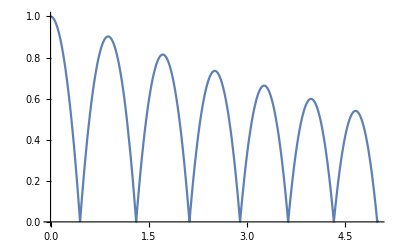

```mathematica
Plot[bb[t],{t,0,5}]
```

The rule x'[t]->−rx[t] specifies that the state variable x'[t] is to be replaced with −rx[t] whenever x[t]=0. After the change is made, the integration is restarted.

An extensive discussion of using WhenEvent can be found in the tutorial Events and Discontinuities in Differential Equations.

```mathematica
Clear["Global`*"]
```

## WhenEvent: Stopping Integration

A ball flying through the air does not follow the ideal parabolic path, but falls short by a significant amount. The cause is referred to as drag, a slowing force proportional to the square of the ball’s velocity exerted by the surrounding air.

### Modeling Velocity and Acceleration

An easy approach is to assume the acceleration can be broken into horizontal and vertical components. This results in a simultaneous system of equations in the functions v_h (horizontal velocity), v_v (vertical velocity), p_h (horizontal position) and p_v (vertical position):

```mathematica
Clear["Global`*"];
```

```mathematica
eqns={vh'[t]== -k vh[t]^2,vv'[t]==-k vv[t]Abs[vv[t]]-g,ph'[t]==vh[t],
pv'[t]==vv[t]};
```

Throw the ball at time t=0 from the origin with velocity v0 at an angle ϕ:

```mathematica
cond={vh[0]==v0 Cos[ϕ],vv[0]==v0 Sin[ϕ],ph[0]==0,pv[0]==0};
```

Define the values for the initial velocity v0, the angle of the throw ϕ, the gravitational constant g, and the constant k representing the drag in air:

```mathematica
v0=20;ϕ=π/4;g=9.81;k=0.01;
```

### Solving

Since you do not know how long it will take until the ball hits the ground, you can use WhenEvent to stop the integration when the vertical position p_v becomes less than 0, i.e. when the ball hits the ground:

```mathematica
solDrag= First@NDSolve[{eqns,cond,WhenEvent[pv[t]<0,{"StopIntegration",tmaxDrag=t}]},
{pv[t],ph[t],vv[t],vh[t]},{t,0,Infinity},MaxSteps->Infinity]
```

{pv[t]→InterpolatingFunction[…][t],ph[t]→InterpolatingFunction[…][t],vv[t]→InterpolatingFunction[…][t],vh[t]→InterpolatingFunction[…][t]}

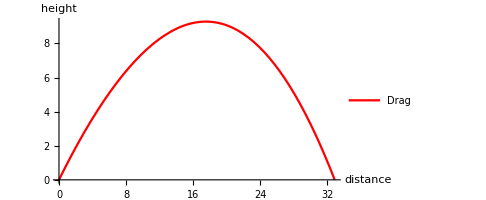

```mathematica
plt=ParametricPlot[Evaluate[{ph[t]/.solDrag,pv[t]/.solDrag}],{t,0,tmaxDrag},AxesLabel->{Style["distance",16],Style["height",16]},ImageSize->Medium,PlotStyle->Red,PlotLegends->{"Drag"}]
```

Compare with the no air resistance result. To do this, set k=0 and re-solve the equation:

```mathematica
k=0;
eqns={vh'[t]==-k vh[t]^2,vv'[t]==-k vv[t] Abs[vv[t]]-g,pv'[t]==vv[t],
ph'[t]==vh[t]};
```

```mathematica
solNoDrag=First@NDSolve[{eqns,cond,WhenEvent[pv[t]<0,{"StopIntegration",tmaxNoDrag=t}]},{pv[t],ph[t],vv[t],vh[t]},{t,0,Infinity}]
```

{pv[t]→InterpolatingFunction[…][t],ph[t]→InterpolatingFunction[…][t],vv[t]→InterpolatingFunction[…][t],vh[t]→InterpolatingFunction[…][t]}

Show both solutions:

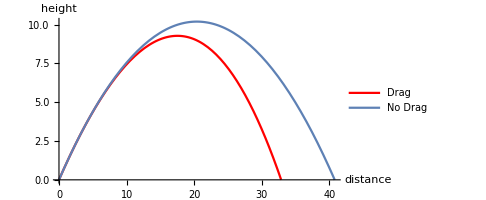

```mathematica
Show[{plt,ParametricPlot[{Evaluate[ph[t]/.solNoDrag],Evaluate[pv[t]/.solNoDrag]},{t,0,tmaxNoDrag},PlotLegends->{"No Drag"}]},PlotRange->All]
```

```mathematica
Clear["Global`*"]
```

```mathematica
sol=NDSolve[{y''[t]+Sin[y[t]]==0,y'[0]==0,y[0]==1,WhenEvent[y[t]==0,{"StopIntegration",tmax=t}]},y[t],{t,0,Infinity},MaxSteps->Infinity][[1]]
```

{y[t]→InterpolatingFunction[…][t]}

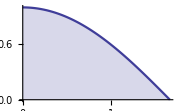

```mathematica
Plot[Evaluate[y[t]/.sol],{t,0,tmax},PlotStyle->ColorData[1][1],Filling->Axis,ImageSize->Small]
```

## Shooting Method

Some differential equations have multiple solutions. However, you may want to find a particular solution among all the solutions. For example:

```mathematica
eqn=x''[t]+Sin[x[t]]==0;
cond={x[0]==0,x[10]==0};
sol=NDSolveValue[{eqn,cond},x[t],{t,0,10}]
```

InterpolatingFunction[…][t]

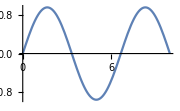

```mathematica
Plot[sol,{t,0,10},ImageSize->Small]
```

The solution satisfies the boundary conditions specified, but imagine that the solution sought is supposed to look something like this:

InterpolatingFunction[…][t]

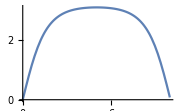

```mathematica
cond={x[0]==0,x'[0]==1.9993};
sol=NDSolveValue[{eqn,cond},x[t],{t,0,10}]
Plot[sol,{t,0,10},ImageSize->Small]
```

This also satisfies the boundary condition of the function going to zero at x=0 and x=10. How do you get this solution?

This is where the "Shooting" method comes into play. You can change the solution that is found by specifying different "StartingInitialConditions".

The boundary conditions are x(0)==x(10)==0. Use x'[0]=1.5, 1.75 and 2 to initialize the "Shooting" method. The "Shooting" method finds the three independent solutions using these three different initializations:

```mathematica
cond={x[0]==x[10]==0};
sol1=NDSolveValue[{eqn,cond},x[t],t,Method->{"Shooting","StartingInitialConditions"->{x'[0]==1.5}}];
sol2=NDSolveValue[{eqn,cond},x[t],t,Method->{"Shooting","StartingInitialConditions"-> {x'[0]==1.75}}];
sol3=NDSolveValue[{eqn,cond},x[t],t,Method->{"Shooting","StartingInitialConditions"-> {x'[0]==2}}];
```

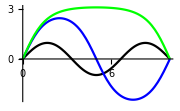

```mathematica
Plot[{sol1,sol2,sol3},{t,0,10},PlotStyle->{Black,Blue,Green},ImageSize->Small]
```

```mathematica
Clear["Global`*"]
```

## NDEigensystem

NDEigensystem solves the eigenvalue problem:

Ô y[x]=λy[x]

Where Ô is some differential operator, and λ are the initially unknown eigenvalues.

Consider the eigenvalue equation: y''[x]+λ y[x]==0. This can be rearranged into the form -y''[x]=λy[x]. Therefore, you can see that the operator Ô is -d^2/dx^2.

To use NDEigensystem, you only need the left-hand side of the preceding equation: Ô y[x]:

```mathematica
op=-y''[x];
cond=DirichletCondition[y[x]==0,True];
```

Using DirichletCondition is a convenient way to specify that the function is zero at all boundaries. The first argument of DirichletCondition defines the value of the function on the boundary, while the second argument being True says that y[x]==0 on all boundaries.

Use NDEigensystem to solve the problem, with the last argument specifying how many eigenvalues and functions to find:

```mathematica
{values,functions}=NDEigensystem[{op,cond},y[x],{x,0,10},4]
```

{{0.0986961,0.394789,0.888325,1.57947},{InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x]}}

The output from NDEigensystem contains two parts. The first part is the list of eigenvalues. These are the values of λ for the corresponding solutions. The solutions themselves are in the second part of the output.

Plotting the solutions shows that they all display the desired property of going to zero both at x=0 and x=10:

```mathematica
legend=Row[{"λ = ",values[[#]]}]&/@Range[4]
```

{λ = 0.0986961,λ = 0.394789,λ = 0.888325,λ = 1.57947}

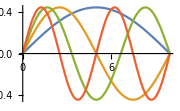

```mathematica
Plot[Evaluate[functions],{x,0,10},PlotLegends->legend,ImageSize->Small]
```

For further information on the methods and options of NDEigensystem, see the documentation.

```mathematica
Clear["Global`*"]
```

## Summary

The Wolfram Language is a powerful tool for working with and solving differential equations. This section of the course covered:

How to specify the numerical method used to solve an equation

Working with stiffness in differential equations

Including events in solutions of differential equations

Solving boundary value problems with the shooting method

Solving eigenvalue problems with NDEigensystem

## Further Reading

#### Tutorials

Advanced Numerical Differential Equation Solving in the Wolfram Language

Numerical Solution of Differential Equations

#### Guides

Differential Equations

Partial Differential Equations

Differential Operators

### Glossary

```mathematica
{{"DirichletCondition", "\"ExplicitRungeKutta\"", "\"ImplicitRungeKutta\"", "NDEigensystem", "NDSolve"}, {"NDSolveValue", "ParametricPlot", "\"Shooting\"", "\"StartingInitialConditions\"", "\"StiffnessSwitching\""}, {"\"StopIntegration\"", "TraditionalForm", "WhenEvent", "", ""}}
```